## Gráficos - Basicão

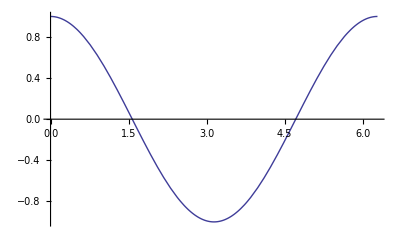

```mathematica
Plot[Cos[x],{x,0,2 π}]
```

◀     |     ▶

## Gráficos - Básico

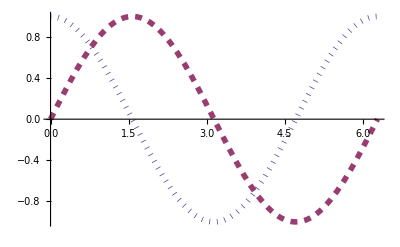

```mathematica
Plot[{Cos[x],Sin[x]},{x,0, 2 π},PlotStyle->{{Dotted, Thickness[0.01]},{Dashed,Thickness[0.01]}}]
```

◀     |     ▶

## Gráficos - Mais Animados

```mathematica
Animate[Plot[{Cos[x+c],Sin[x-c],Cos[x+c]+Sin[x-c]},{x,0,2 π}],{c,0,10,0.1}]
```

◀     |     ▶

## Filling

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,3},Filling->{1->{2}},FillingStyle->LightBrown]
```

## Exercício

Represente graficamente as funçoes de Bessel: J_o, J_1 ... J_7.Descubra como usar Legendas e indique cada uma das funções no gráfico. 

Leia a página do manual sobre Esquemas de Cores (p. ex. Colordata) e liberte sua criatividade. 

Experimente com diferentes espessuar de linhas e formatos para as linhas.

## Exercício

Faça o gráfico de sin(1/x) entre (-2,2) e aumente a quantidade de pontos. Dica use o comando  FullForm e o Help.

## Dados

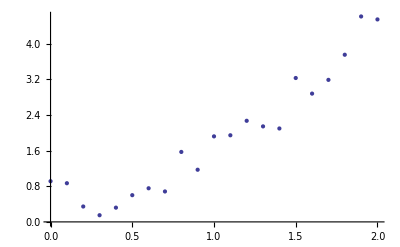

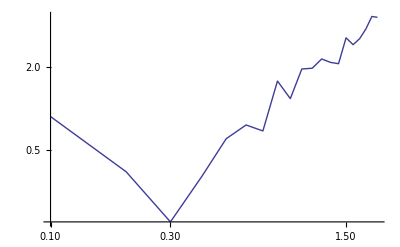

```mathematica
lis=Table[{x,Random[]+x^2},{x,0,2,0.1}];
ListPlot[lis]
ListLogLogPlot[lis,Joined->True]
```

◀     |     ▶

## Exercício

Gere 100 matrizes aleatórias com coeficientes entre -1 e 1 Faça um gráfico onde cada ponto representa 
o Determinante (eixo y) e o Traço (o eixo x).  Represente com cores diferentes os pontos dependendo do número de autovalores reais que a Matriz possui. 

Interprete o gráfico, encontre a equação da curva que separa os regimes.

## Juntando Gráficos

Suponha que você precise juntar gráficos produzidos de diferentes formas. Por exemplo um conjunto de dados experimentais e uma função de ajuste.

```mathematica
gr1=ListLogPlot[Reverse[Sort[CountryData[#,"Population"]&/@CountryData[]]]];
```

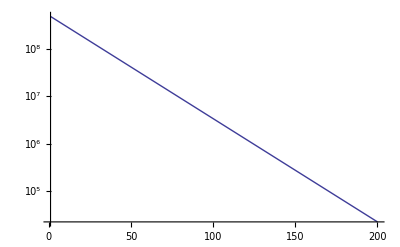

```mathematica
gr2=LogPlot[5 10^8 Exp[-0.05 t],{t,1,200}]
```

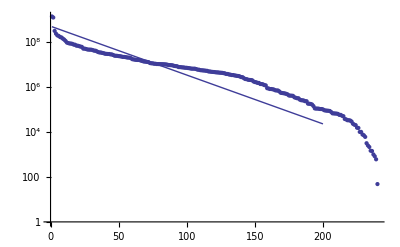

```mathematica
Show[gr1,gr2]
```

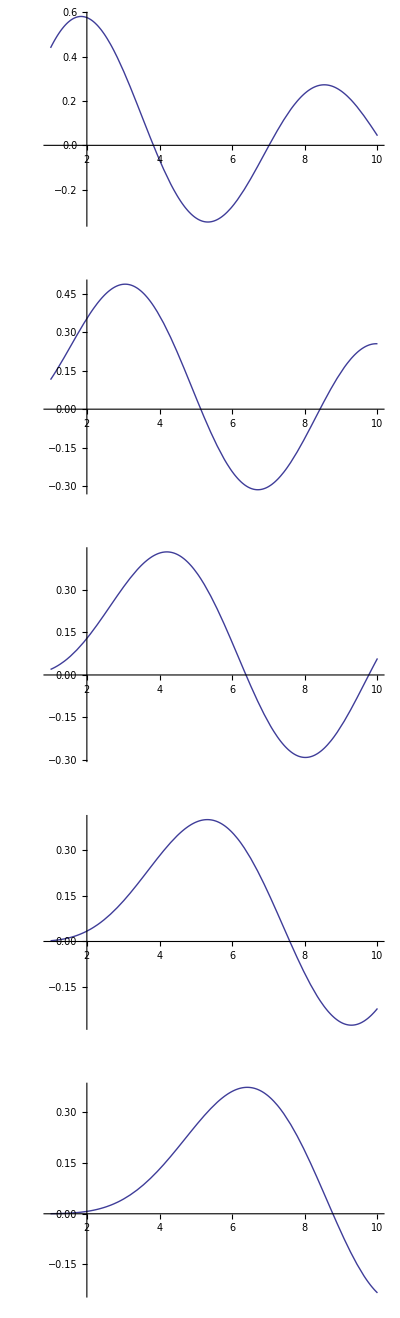

```mathematica
GraphicsColumn[Table[Plot[BesselJ[n,x],{x,1,10}],{n,1,5}]]
```

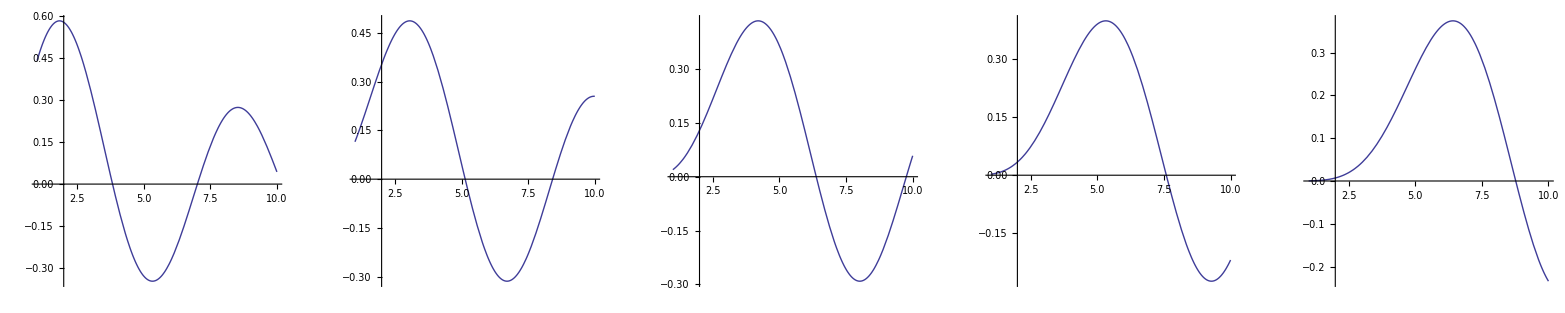

```mathematica
GraphicsRow[Table[Plot[BesselJ[n,x],{x,1,10}],{n,1,5}]]
```

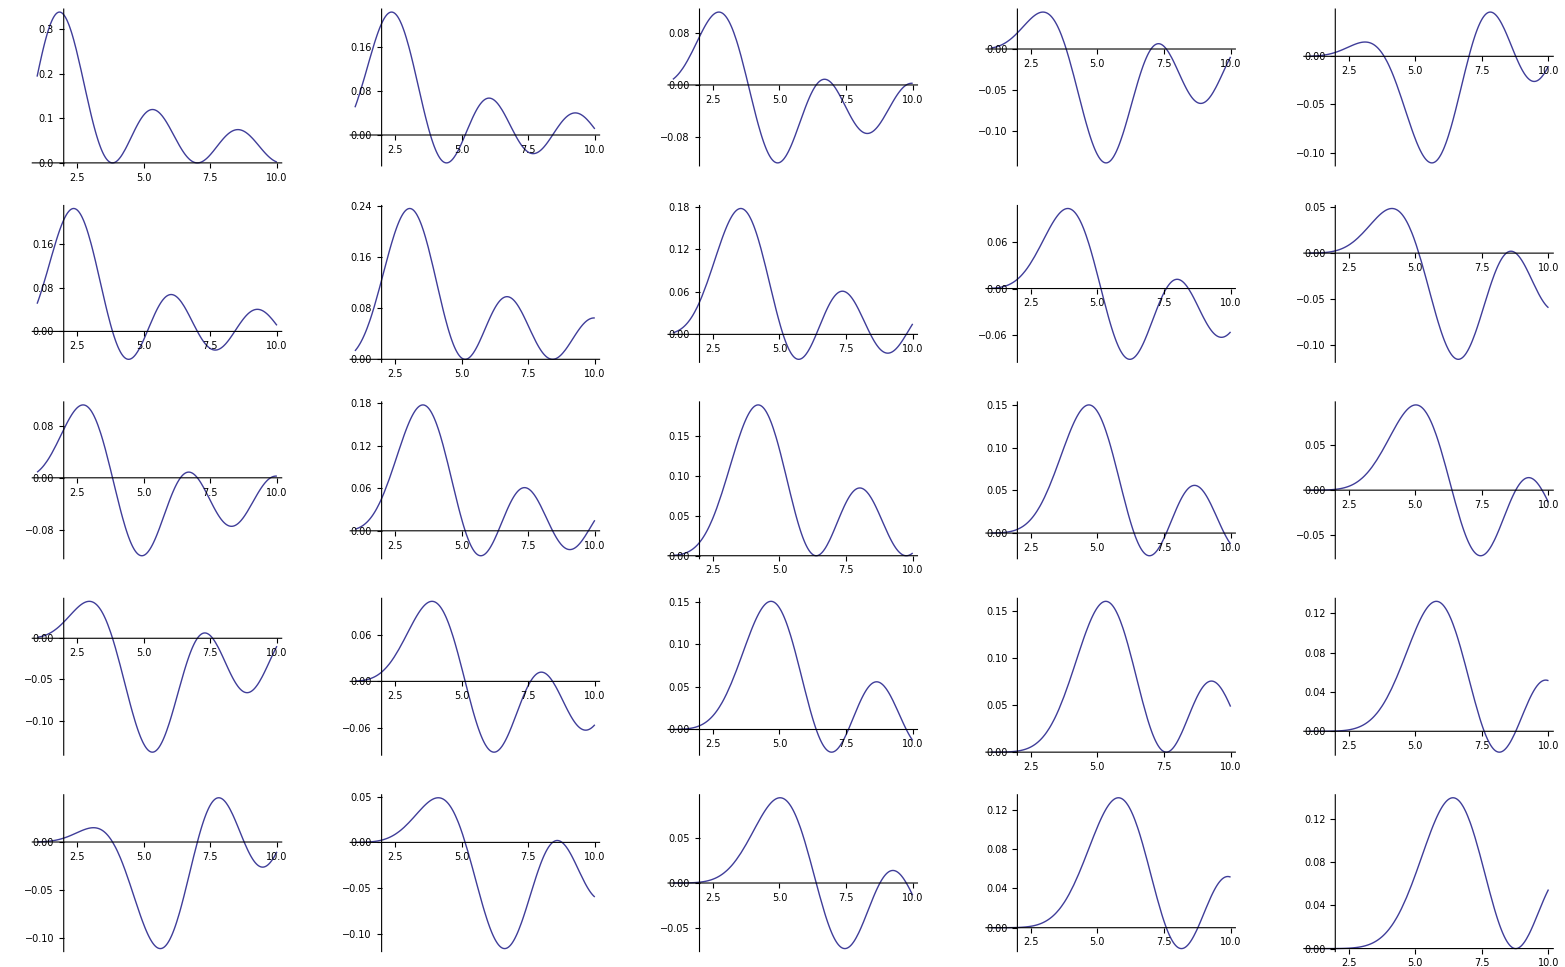

```mathematica
GraphicsGrid[Table[Plot[BesselJ[n,x]*BesselJ[k,x],{x,1,10}],{n,1,5},{k,1,5}]]
```

## Gráficos - 3D

```mathematica
Plot3D[Cos[x+y],{x,0,2 π},{y,0, 2 π}]
```

-Graphics3D-

◀     |     ▶

## Densidade

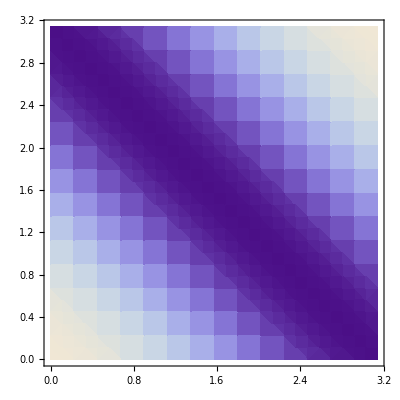

```mathematica
DensityPlot[Cos[x+y],{x,0,π},{y, 0, π}]
```

◀     |     ▶

## Densidade

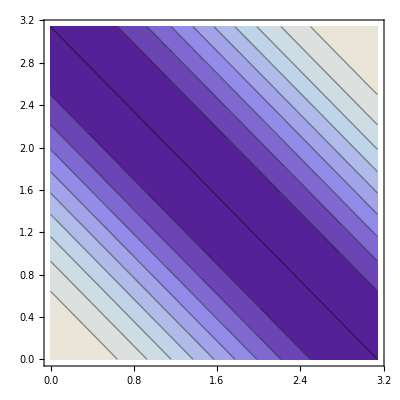

```mathematica
ContourPlot[Cos[x+y],{x,0,π},{y, 0, π}]
```

◀     |     ▶

## Gráficos Bizarros

```mathematica
ContourPlot3D[x^3+y^2-z^2==0,{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

◀     |     ▶

## Regiões

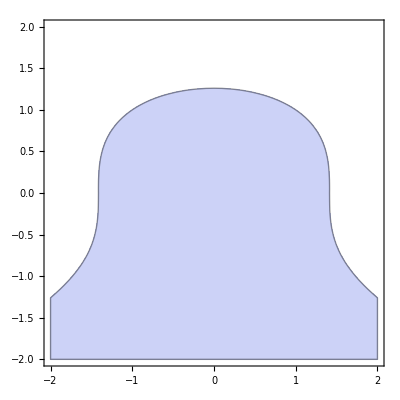

```mathematica
RegionPlot[x^2+y^3<2,{x,-2,2},{y,-2,2}]
```

◀     |     ▶

## Exercício

Faça o gráfico de um esfera colorindo de forma diferente, a região polar, a região tropical e a região equatorial, cada uma com uma cor diferente.

Represente um Tórus

## Nós

```mathematica
KnotData["Trefoil"]
```

-Graphics3D-

◀     |     ▶

## Grafos

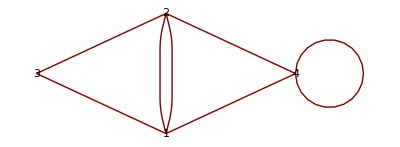

```mathematica
GraphPlot[{1->2,2->1,3->1,3->2,4->1,4->2,4->4},VertexLabeling->True]
```

◀     |     ▶

## Exercício

Construa um grafo cujos os nodos são os países da America do Sul e as arestas indicam se um país faz fronteira com o outro. Desafio tente usar as bandeiras de cada país como sendo a representação do nodo.

## Polihedros

```mathematica
PolyhedronData["Dodecahedron"]
```

-Graphics3D-

◀     |     ▶

## Coisas Legais

```mathematica
Slider[Dynamic[c],{-2,4}]
Slider[Dynamic[a],{-2,2}]
gr1=ListPlot[lis];
Dynamic[ListPlot[{lis,Table[{x,x^c+a},{x,0,2,0.1}]},PlotStyle->{Joined->False,Joined->True}]]
```

◀     |     ▶

## Coisas Legais

```mathematica
Manipulate[Plot[Sin[a x+b],{x,0,6}],{{a,2,"Multiplier"},1,4},{{b,0,"Phase Parameter"},0,10}]
```

◀     |     ▶

## Coisas Muito Legais

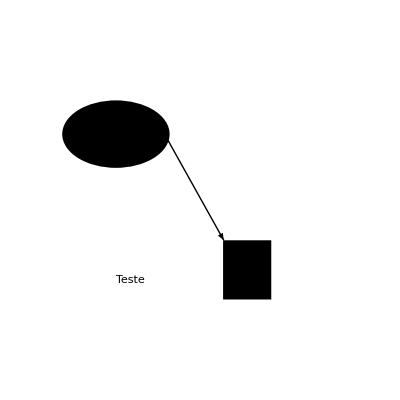
```mathematica
gr1=-Graphics-
```

-Graphics-

```mathematica
gr1//FullForm
```

Graphics[List[Disk[List[0.241268,0.703055],List[0.164232,0.103171]],Rectangle[List[0.570601,0.37676],List[0.717989,0.195684]],Arrow[List[List[0.400053,0.686275],List[0.572707,0.37676]]],List[GrayLevel[0],AbsolutePointSize[3],AbsoluteThickness[0.5],Opacity[1],Dashing[List[]],Arrowheads[0.04],EdgeForm[None],Inset[Cell["Teste"],List[0.24207,0.254678],List[-1.,0.]]]],Rule[PlotRange,List[List[0,1],List[0,1]]]]

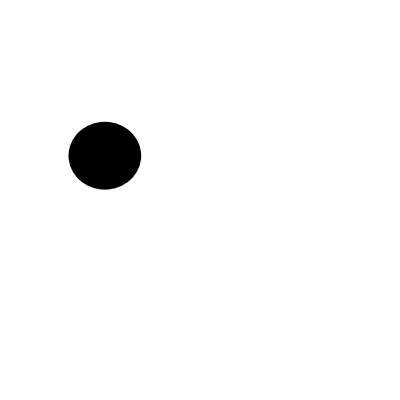
```mathematica
gr2=-Graphics-
```

-Graphics-

```mathematica
gr2//FullForm
```

Graphics[List[GrayLevel[0],Opacity[1],EdgeForm[None],Disk[List[0.207407,0.637037],List[0.111111,0.103704]]],Rule[PlotRange,List[List[0,1],List[0,1]]]]

```mathematica
Slider[Dynamic[c],{0,4}]
Dynamic[Graphics[List[GrayLevel[0],Opacity[1],EdgeForm[None],Disk[List[0.20740740740740726+c,0.6370370370370371],List[0.11111111111111105+c,0.10370370370370374]]],Rule[PlotRange,List[List[0,1],List[0,1]]]]]
```

◀     |     ▶

## Animação

Monte uma pequena animação gerando um desenho usando o editor de gráficos e variando, posição e 
cores dos objetos. A animação mais legal vai receber o prestigioso prêmio Framboesa de Ouro versão Botucatu. A escolha será feita por aclamação.